```mathematica
(* dimensione dei blocchi su cui applicare la sostituzione *)
l=4
(* numero di blocchi *)
m=4

sbox="E4D12FB83A6C5907"
IntegerDigits[FromDigits[sbox,16],16,16]
permutation={1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

S[x_]:=IntegerDigits[FromDigits[sbox,16],16,16][[x+1]]
P[x_]:=Map[FromDigits[#,2]&,Partition[Flatten[Map[IntegerDigits[#,2,4]&,x]][[permutation]],4]]
AddKey[x_,k_]:=MapThread[BitXor,{x,k}]
```

4

4

E4D12FB83A6C5907

{14,4,13,1,2,15,11,8,3,10,6,12,5,9,0,7}

{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

```mathematica
ScalarP[a_,x_]:=Plus@@(IntegerDigits[a,2,4]*IntegerDigits[x,2,4])
ScalarP2[a_,x_]:=Mod[DigitCount[BitAnd[a,x],2,1],2]
NL[a_,b_]:=Plus@@Table[Mod[ScalarP[a,x]+ScalarP[b,S[x]],2],{x,0,15}]
```

```mathematica
epsilon[a_,b_]:=NL[a,b]/2^l-1/2
```

```mathematica
TableForm@(NLT=Table[NL[a,b],{a,0,2^l},{b,0,2^l}])
```

0 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 0
8 | 8 | 10 | 10 | 8 | 8 | 10 | 2 | 6 | 6 | 8 | 8 | 6 | 6 | 8 | 8 | 8
8 | 8 | 10 | 10 | 8 | 8 | 10 | 10 | 8 | 8 | 6 | 6 | 8 | 8 | 14 | 6 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 6 | 14 | 10 | 10 | 6 | 6 | 10 | 10 | 8
8 | 6 | 8 | 10 | 10 | 12 | 10 | 8 | 8 | 10 | 8 | 6 | 6 | 12 | 6 | 8 | 8
8 | 10 | 10 | 8 | 10 | 8 | 4 | 6 | 10 | 8 | 12 | 6 | 8 | 10 | 10 | 8 | 8
8 | 6 | 10 | 4 | 6 | 8 | 8 | 6 | 8 | 10 | 6 | 4 | 10 | 8 | 8 | 10 | 8
8 | 10 | 8 | 6 | 6 | 12 | 6 | 8 | 10 | 8 | 6 | 8 | 4 | 6 | 8 | 6 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 10 | 6 | 6 | 10 | 6 | 10 | 10 | 14 | 8
8 | 8 | 10 | 10 | 8 | 8 | 10 | 10 | 12 | 8 | 10 | 6 | 8 | 4 | 6 | 10 | 8
8 | 4 | 10 | 6 | 12 | 8 | 6 | 10 | 6 | 6 | 8 | 8 | 6 | 6 | 8 | 8 | 8
8 | 4 | 8 | 12 | 4 | 8 | 4 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 10 | 4 | 10 | 10 | 8 | 6 | 8 | 6 | 8 | 6 | 4 | 8 | 6 | 8 | 10 | 8
8 | 6 | 6 | 8 | 10 | 4 | 8 | 6 | 12 | 10 | 6 | 8 | 6 | 8 | 8 | 6 | 8
8 | 6 | 6 | 8 | 10 | 12 | 8 | 6 | 10 | 8 | 8 | 10 | 12 | 6 | 10 | 8 | 8
8 | 10 | 12 | 10 | 10 | 8 | 6 | 8 | 8 | 10 | 4 | 10 | 10 | 8 | 6 | 8 | 8
0 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 0

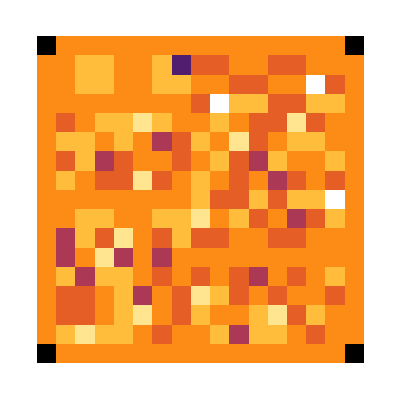

```mathematica
ArrayPlot[NLT,ColorFunction->"SunsetColors"]
```

```mathematica
ND[deltax_,deltay_]:=
```

```mathematica
deltax=11
TableForm@
Table[{x,x1=BitXor[x,deltax],S[x],S[x1],BitXor[S[x],S[x1]]},{x,0,2^l-1}]
```

11

0 | 11 | 14 | 12 | 2
1 | 10 | 4 | 6 | 2
2 | 9 | 13 | 10 | 7
3 | 8 | 1 | 3 | 2
4 | 15 | 2 | 7 | 5
5 | 14 | 15 | 0 | 15
6 | 13 | 11 | 9 | 2
7 | 12 | 8 | 5 | 13
8 | 3 | 3 | 1 | 2
9 | 2 | 10 | 13 | 7
10 | 1 | 6 | 4 | 2
11 | 0 | 12 | 14 | 2
12 | 7 | 5 | 8 | 13
13 | 6 | 9 | 11 | 2
14 | 5 | 0 | 15 | 15
15 | 4 | 7 | 2 | 5

```mathematica
sbox="E4D12FB83A6C5907"
```

E4D12FB83A6C5907

```mathematica
deltax
admissible=Tally[Table[BitXor[S[x],S[BitXor[x,deltax]]],{x,0,2^l-1}]]
```

11

{{2,8},{7,2},{5,2},{15,2},{13,2}}

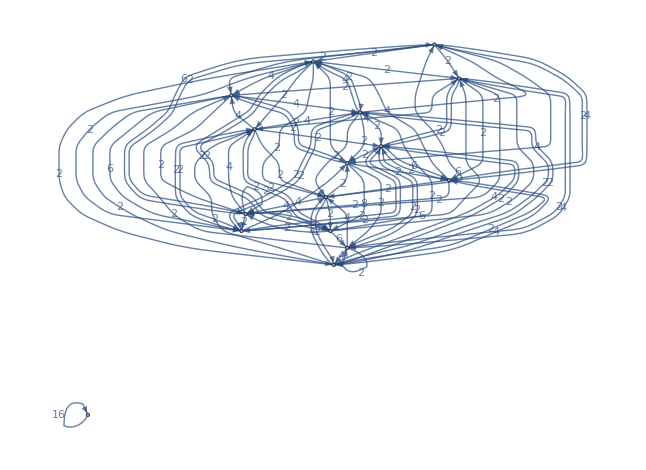

```mathematica
LayeredGraphPlot@Graph@
Flatten[Table[
admissible=Tally[Table[BitXor[S[x],S[BitXor[x,deltax]]],{x,0,2^l-1}]];
Map[Labeled[deltax->#[[1]],#[[2]]]&,admissible],
{deltax,0,2^l-1}]]
```

```mathematica
2^16
```

65536

```mathematica
ndsparse=SparseArray@Flatten@Table[
admissible=Tally[Table[BitXor[S[x],S[BitXor[x,deltax]]],{x,0,2^l-1}]];
Map[(1+{deltax,#[[1]]})->#[[2]]&,admissible],
{deltax,0,2^l-1}]
```

SparseArray[…]

```mathematica
Normal[ndsparse]
```

{{16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,2,0,0,0,2,0,2,4,0,4,2,0,0},{0,0,0,2,0,6,2,2,0,2,0,0,0,0,2,0},{0,0,2,0,2,0,0,0,0,4,2,0,2,0,0,4},{0,0,0,2,0,0,6,0,0,2,0,4,2,0,0,0},{0,4,0,0,0,2,2,0,0,0,4,0,2,0,0,2},{0,0,0,4,0,4,0,0,0,0,0,0,2,2,2,2},{0,0,2,2,2,0,2,0,0,2,2,0,0,0,0,4},{0,0,0,0,0,0,2,2,0,0,0,4,0,4,2,2},{0,2,0,0,2,0,0,4,2,0,2,2,2,0,0,0},{0,2,2,0,0,0,0,0,6,0,0,2,0,0,4,0},{0,0,8,0,0,2,0,2,0,0,0,0,0,2,0,2},{0,2,0,0,2,2,2,0,0,0,0,2,0,6,0,0},{0,4,0,0,0,0,0,4,2,0,2,0,2,0,2,0},{0,0,2,4,2,0,0,0,6,0,0,0,0,0,2,0},{0,2,0,0,6,0,0,0,0,4,0,2,0,0,2,0}}